```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];
Get["filegrabber.m"]
```

```mathematica
getOptCheckFN[mode_Integer, numThreads_Integer, numQubits_Integer] :=
	getFilename[
		StringJoin["instMode", ToString[mode], "_results"],
		"ProjectQ", numThreads, 100, numQubits
	]
```

```mathematica
getOptCheckFN[4, 16, 30]
```

Python/instMode4_results/ARC_ProjectQ/threads16/depth100/qubits30.txt

```mathematica
optDurs[mode_Integer, numThreads_Integer] := N @ Table[Mean @ Get[getOptCheckFN[mode, numThreads, numQubits]]["durations"], {numQubits,Range[1,30]}]
```

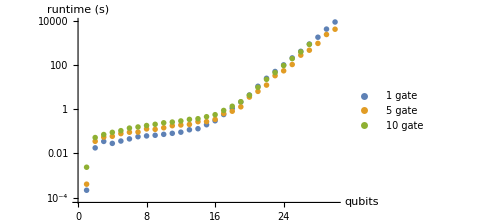
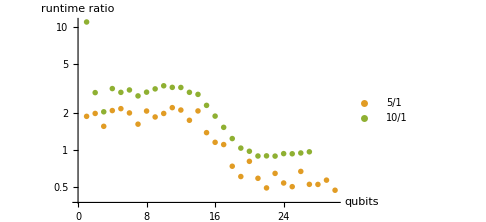
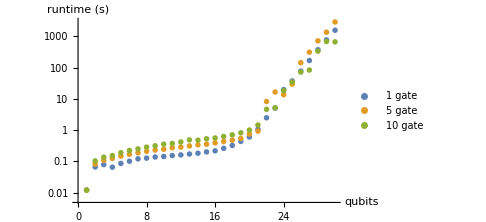
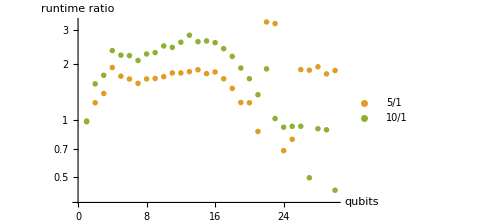
-Graphics-
-Graphics-1 threads-Graphics-
-Graphics-16 threads

```mathematica
optSpeedupPlot = Row @ Table[
	Column @ {
	ListLogPlot[
		{optDurs[4, nthreads], optDurs[5, nthreads], optDurs[6, nthreads]},
		AxesLabel -> {"qubits", "runtime (s)"},
		ImageSize-> Medium, PlotLegends-> Placed[{"1 gate", "5 gate", "10 gate"}, Above],
		PlotStyle->({#1}& /@ ColorData[97, "ColorList"][[1;;3]])
	], 
	Labeled[#, StringJoin[ToString @ nthreads, " threads"]]& @ ListLogPlot[
		{optDurs[5, nthreads] / optDurs[4, nthreads], optDurs[6, nthreads] / optDurs[4, nthreads]},
		ImageSize-> Medium, PlotLegends-> Placed[{"5/1", "10/1"}, Above],
		GridLines-> {{}, {1, 2}}, AxesLabel->{"qubits", "runtime ratio"},
		PlotStyle->({#1}& /@ ColorData[97, "ColorList"][[2;;3]])
	]
	},
	{nthreads, {1,16}}
]
```

Sometimes 5gate cache outperforms 1gate (especially on single thread); LocalOptimization is occurring for our random circuits.

```mathematica
(* Export["RandomCircuitDepth100OptimizerSpeedup.pdf", optSpeedupPlot] *)
```